```mathematica
f[a_,u_,v_,m_,H_]:=a/2*m^2+u/4*m^4+v/6*m^6-m*H
v:=1
u:=-1
```

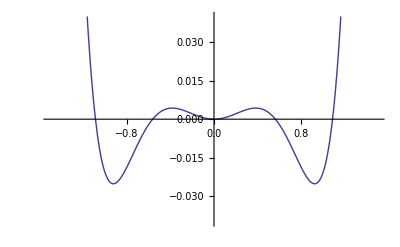
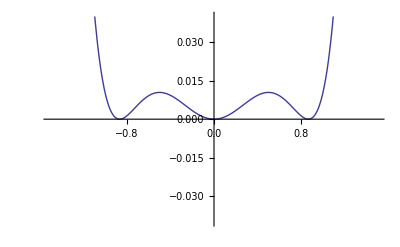
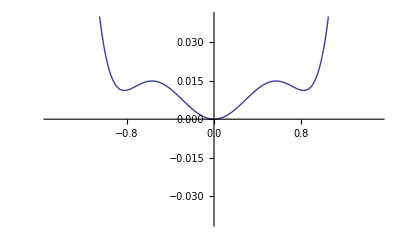

```mathematica
Table[Plot[f[a,u,v,m,0],{m,-1.5,1.5},PlotRange->0.04],{a,{2/16,3/16,3.5/16}}]
```

```mathematica
Export["~/Dokumentumok/elsorendu0.pdf",Plot[f[2/16,u,v,m,0],{m,-1.5,1.5},PlotRange->0.04,PlotStyle->{Thick},AxesLabel->{Style["m",15,Black,FontFamily->"ComputerModern"],Style["F",15,Black,FontFamily->"ComputerModern"]}]]
Export["~/Dokumentumok/elsorendu1.pdf",Plot[f[3/16,u,v,m,0],{m,-1.5,1.5},PlotRange->0.04,PlotStyle->{Thick},AxesLabel->{Style["m",15,Black,FontFamily->"ComputerModern"],Style["F",15,Black,FontFamily->"ComputerModern"]}]]
Export["~/Dokumentumok/elsorendu2.pdf",Plot[f[3.5/16,u,v,m,0],{m,-1.5,1.5},PlotRange->0.04,PlotStyle->{Thick},AxesLabel->{Style["m",15,Black,FontFamily->"ComputerModern"],Style["F",15,Black,FontFamily->"ComputerModern"]}]]
```

~/Dokumentumok/elsorendu0.pdf

~/Dokumentumok/elsorendu1.pdf

~/Dokumentumok/elsorendu2.pdf

```mathematica
solp=Solve[(p[V,T]+3/V^2)*(3*V-1)==8*T,p[V,T]]
```

{{p[V,T]→(3-9 V+8 T V^2)/(V^2 (-1+3 V))}}

```mathematica
p[v_,t_]:=8t/(3*v-1)-3/v^2
```

```mathematica
sol1=Solve[{D[8t/(3*v-1)-3/v^2,v]==0},v];
```

```mathematica
vmidle[tt_]:=((Min[Re[v/.sol1[[1]]],Re[v/.sol1[[2]]],Re[v/.sol1[[3]]]]+Max[Re[v/.sol1[[1]]],Re[v/.sol1[[2]]],Re[v/.sol1[[3]]]])/.t->tt)/2
```

```mathematica
sol2=Solve[{p[v,t]==p[vmidle[t],t]},v];
```

```mathematica
szamolo[tt_]:=(ttt=tt;
vvv1=(Min[Re[v/.sol2[[1]]],Re[v/.sol2[[2]]],Re[v/.sol2[[3]]]]/.t->ttt);
vvv3=(Max[Re[v/.sol2[[1]]],Re[v/.sol2[[2]]],Re[v/.sol2[[3]]]]/.t->ttt);
vvvmidle=vmidle[ttt];
For[i=0,i<15,i++,
If[p[vvv3,ttt]*(vvv3-vvv1)<Re[Integrate[p[v,ttt],{v,vvv1,vvv3}]],vvvmidle+=0.1,vvvmidle-=0.1];
sol3=Solve[{p[v,ttt]==p[vvvmidle,ttt]},v];
vvv1=(Min[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
vvv3=(Max[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
]
For[i=0,i<10,i++,
If[p[vvv3,ttt]*(vvv3-vvv1)<Re[Integrate[p[v,ttt],{v,vvv1,vvv3}]],vvvmidle+=0.01,vvvmidle-=0.01];
sol3=Solve[{p[v,ttt]==p[vvvmidle,ttt]},v];
vvv1=(Min[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
vvv3=(Max[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
]
For[i=0,i<10,i++,
If[p[vvv3,ttt]*(vvv3-vvv1)<Re[Integrate[p[v,ttt],{v,vvv1,vvv3}]],vvvmidle+=0.001,vvvmidle-=0.001];
sol3=Solve[{p[v,ttt]==p[vvvmidle,ttt]},v];
vvv1=(Min[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
vvv3=(Max[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
]
For[i=0,i<10,i++,
If[p[vvv3,ttt]*(vvv3-vvv1)<Re[Integrate[p[v,ttt],{v,vvv1,vvv3}]],vvvmidle+=0.0001,vvvmidle-=0.0001];
sol3=Solve[{p[v,ttt]==p[vvvmidle,ttt]},v];
vvv1u=(Min[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
vvv3u=(Max[Re[v/.sol3[[1]]],Re[v/.sol3[[2]]],Re[v/.sol3[[3]]]]);
dv1=vvv1-vvv1u;
dv3=vvv3-vvv3u;
vvv1=vvv1u;
vvv3=vvv3u;
];
Print[{vvv1,vvv3,(Integrate[p[v,ttt],{v,vvv1,vvv3}]-p[vvv1,ttt]*(vvv3-vvv1))/(p[vvv1,ttt]*(vvv3-vvv1))}];)
```

```mathematica
Table[szamolo[n],{n,{0.95,0.9,0.85,0.8}}]
```

{0.684115,1.72697,-0.0000172349+0. ⅈ}

{0.603404,2.34893,0.0000171708+0. ⅈ}

{0.553361,3.12773,0.0000172708+0. ⅈ}

{0.51741,4.17274,0.0000458955+0. ⅈ}

{Null,Null,Null,Null}

```mathematica
szamolo[0.99]
```

{0.740859,1.10011,-0.0476353+0. ⅈ}

```mathematica
valodi095[v_]:=If[v<0.6841145443263493||v>1.7269708524490643,p[v,0.95],p[1.7269708524490643,0.95]];
valodi09[v_]:=If[v<0.6034038892507049||v>2.3489293206233057,p[v,0.9],p[2.3489293206233057,0.9]];
valodi085[v_]:=If[v<0.5533612221373666||v>3.127731813653345,p[v,0.85],p[3.127731813653345,0.85]];
valodi08[v_]:=If[v<0.5174102112994196||v>4.172740462013345,p[v,0.8],p[4.172740462013345,0.8]];
valodi075[v_]:=If[v<0.4896325086157406||v>5.644183735616454,p[v,0.75],p[5.644183735616454,0.75]];
valodi07[v_]:=If[v<0.46719371793287034||v>7.812475977377699,p[v,0.70],p[7.812475977377699,0.70]];
valodi065[v_]:=If[v<0.44851164583945413||v>11.177529641348427,p[v,0.65],p[11.177529641348427,0.65]];
```

```mathematica
bordera=Fit[{{0.44851164583945413,p[11.177529641348427,0.65]},{0.46719371793287034,p[7.812475977377699,0.70]},{0.4896325086157406,p[5.644183735616454,0.75]},{0.5174102112994196,p[4.172740462013345,0.8]},{0.5533612221373666,p[3.127731813653345,0.85]},{0.6034038892507049,p[2.3489293206233057,0.9]},{0.6841145443263493,p[1.7269708524490643,0.95]},{0.7408589354302464,p[1.1001147439681813,0.99]},{1,1},{1.1001147439681813,p[1.1001147439681813,0.99]},{1.7269708524490643,p[1.7269708524490643,0.95]},{2.3489293206233057,p[2.3489293206233057,0.9]},{3.127731813653345,p[3.127731813653345,0.85]},{4.172740462013345,p[4.172740462013345,0.8]},{5.644183735616454,p[5.644183735616454,0.75]},{7.812475977377699,p[7.812475977377699,0.70]},{11.177529641348427,p[11.177529641348427,0.65]}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

-4.53582+18.3738 x-23.8745 x^2+15.9368 x^3-6.08494 x^4+1.36596 x^5-0.17646 x^6+0.0120197 x^7-0.000331181 x^8

```mathematica
Show[Plot[bordera,{x,1/3,5}],ListPlot[{{0.6841145443263493,p[1.7269708524490643,0.95]},{1.7269708524490643,p[1.7269708524490643,0.95]},{0.6034038892507049,p[2.3489293206233057,0.9]},{2.3489293206233057,p[2.3489293206233057,0.9]},{0.5533612221373666,p[3.127731813653345,0.85]},{3.127731813653345,p[3.127731813653345,0.85]},{0.5174102112994196,p[4.172740462013345,0.8]},{4.172740462013345,p[4.172740462013345,0.8]},{0.4896325086157406,p[5.644183735616454,0.75]},{5.644183735616454,p[5.644183735616454,0.75]},{0.46719371793287034,p[7.812475977377699,0.70]},{7.812475977377699,p[7.812475977377699,0.70]},{0.44851164583945413,p[11.177529641348427,0.65]},{11.177529641348427,p[11.177529641348427,0.65]},{0.7408589354302464,p[1.1001147439681813,0.99]},{1.1001147439681813,p[1.1001147439681813,0.99]},{1,1}},DataRange->{1/3,5}]]
```

```mathematica
Export["~/Dokumentumok/valodivdW.pdf",Show[
Plot[{-3/v^2+(2 (-1+3 v))/v^3},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Orange,Thick},AxesOrigin->{0,0},AxesLabel->{Style["V",15,Black,FontFamily->"ComputerModern"],Style["p",15,Black,FontFamily->"ComputerModern"]}],Plot[{valodi095[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],
Plot[{valodi09[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],Plot[{valodi085[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],
Plot[{valodi08[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],
Plot[{valodi075[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],Plot[{valodi07[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],
Plot[{valodi065[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],
Table[Plot[p[v,t],{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0},AxesLabel->{Style["V",15,Black,FontFamily->"ComputerModern"],Style["p",15,Black,FontFamily->"ComputerModern"]}],{t,1,3,0.1}]]]
```

~/Dokumentumok/valodivdW.pdf

```mathematica
Export["~/Dokumentumok/direktvdW.pdf",Show[
Plot[{-3/v^2+(2 (-1+3 v))/v^3},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Orange,Thick},AxesOrigin->{0,0},AxesLabel->{Style["V",15,Black,FontFamily->"ComputerModern"],Style["p",15,Black,FontFamily->"ComputerModern"]}],
Table[Plot[p[v,t],{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Blue,Thick},AxesOrigin->{0,0}],{t,0.4,3,0.075}]]]
```

~/Dokumentumok/direktvdW.pdf

```mathematica
Export["~/Dokumentumok/Mxkonstr.pdf",Show[
Plot[{-3/v^2+(2 (-1+3 v))/v^3},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{Orange,Thick},AxesOrigin->{0,0},AxesLabel->{Style["V",15,Black,FontFamily->"ComputerModern"],Style["p",15,Black,FontFamily->"ComputerModern"]}],
Plot[{p[v,0.85],valodi085[v]},{v,1/3,5},PlotRange->{0,1.5},PlotStyle->{{Blue,Thick},{Blue,Thick}},Filling->{1->{2}},AxesOrigin->{0,0}]]]
```

~/Dokumentumok/Mxkonstr.pdf

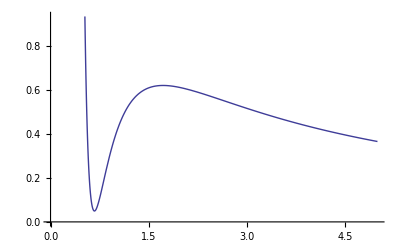

```mathematica
Plot[{p[v,0.85],Integrate[p[vv,0.85],vv]/.vv->v},{v,1/3,5},AxesOrigin->{0,0}]
```

```mathematica
Integrate[p[v,0.85],v]
```

3/v+2.26667 Log[1.-3. v]

```mathematica
Integrate[p[vv,0.85],{vv,1/3,vvv}]/.vvv->v
```

Integrate::idiv: Integral of -6.8/1 - 3\ vv - 3/vv^2 does not converge on {1/3, vvv}.

Integrate::idiv: Integral of -6.8/1 - 3\ vv - 3/vv^2 does not converge on {1/3, v}.

```mathematica
soll=Solve[p[v,0.85]==pp,v];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

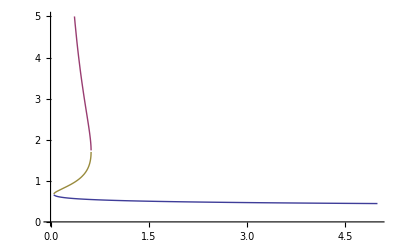

```mathematica
Plot[{v/.soll[[1]]/.pp->p,v/.soll[[2]]/.pp->p,v/.soll[[3]]/.pp->p},{p,0,5},PlotRange->{0,5}]
```